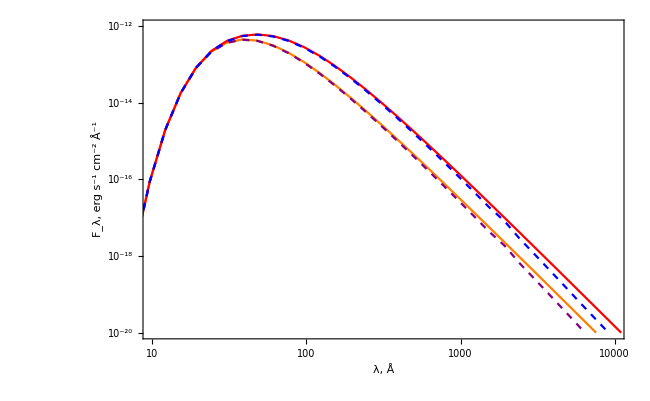

```mathematica
Clear["Global`*"]

(*Множитель красного смещения*)
R0=12;
zFactor=Sqrt[(1-(4.134/R0))];


(*Импорт данных*)
mixingResult = Import["C:\\Users\\Алексей\\Documents\\Axions_RXJ_Paper\\References_for_paper\\Mixing_data\\Mixing_data.dat"];
energyInfLog=mixingResult[[All,1]];
mixingValuesEv = mixingResult[[All,2]];


(*Строим ω с красным смещением*)
energyInf=10^x/.x->energyInfLog;
energySurf=energyInf/zFactor;

energyValues=energyInf;

wavelengthValues=Reverse[2 Pi/#*1.97*10^3&/@energyValues];
mixingValuesA=Reverse[ mixingResult[[All,2]]];

(*Print[energyValues,wavelengthValues]*)

(*Поглощение на водороде*)
(*Коэффициенты кривой поглощения*)
c0[x_]:=Piecewise[{
{17.3,0.030<x<=0.100},
	{34.6,0.100<=x<0.284},
	{78.1,0.284<=x<0.400},
{71.4,0.400<=x<0.532},
	{95.5,0.532<=x<0.707},
	{308.9,0.707<=x<0.867},
	{120.6,0.867<=x<1.303},
	{141.3,1.303<=x<1.840},
	{202.7,1.840<=x<2.471},
	{342.7,2.471<=x<3.210},
	{352.2,3.210<=x<4.038},
	{433.9,4.038<=x<7.111},
	{629.0,7.111<=x<8.331},
	{701.2,8.331<=x<10.000}},0];
c1[x_]:=Piecewise[{
{608.1,0.030<x<=0.100},
	{267.9,0.100<=x<0.284},
	{18.8,0.284<=x<0.400},
{66.8,0.400<=x<0.532},
	{145.8,0.532<=x<0.707},
	{-380.6,0.707<=x<0.867},
	{169.3,0.867<=x<1.303},
	{146.8,1.303<=x<1.840},
	{104.7,1.840<=x<2.471},
	{18.7,2.471<=x<3.210},
	{18.7,3.210<=x<4.038},
	{-2.4,4.038<=x<7.111},
	{30.9,7.111<=x<8.331},
	{25.2,8.331<=x<10.000}},0];
c2[x_]:=Piecewise[{
{-2150.,0.030<x<=0.100},
	{-476.1,0.100<=x<0.284},
	{4.3,0.284<=x<0.400},
{-51.4,0.400<=x<0.532},
	{-61.1,0.532<=x<0.707},
	{294.0,0.707<=x<0.867},
	{-47.7,0.867<=x<1.303},
	{-31.5,1.303<=x<1.840},
	{-17.0,1.840<=x<2.471},
	{0.0,2.471<=x<3.210},
	{0.0,3.210<=x<4.038},
	{0.75,4.038<=x<7.111},
	{0.0,7.111<=x<8.331},
	{0.0,8.331<=x<10.000}},0];

(*Сигма, кол-во атомов водорода *)
sigma[energy_]:=(c0 [energy]energy+c1[energy] energy+c2[energy] energy^2)energy^(-3)*10^(-24);
Nh:=12.9*10^(19);

(*Кривая поглощения, переводим энергию в keV*)
extinctionCurve[energyEv_]:=Exp[-sigma[energyEv*0.001]*Nh];

(*Modification factor для поглощения*)
adsorbtionValues:=extinctionCurve/@energyValues;


(*Поглощение на пыли*)
(*Коэффициенты кривой поглощения*)

Fa[x_]:=Piecewise[ {{-0.04473(x-5.9)^2-0.009779(x-5.9)^3, 5.9≤x≤8}},
0];
Fb[x_]:=Piecewise[ {{0.2130(x-5.9)^2+0.1207(x-5.9)^3, 5.9≤x≤8}},
0];

a[x_]:=Piecewise[{
{0.574 x^(1.61),0.3<=x<1.1},
	{1+0.104*(x-1.82)-0.609*(x-1.82)^2+0.701*(x-1.82)^3+1.137*(x-1.82)^4-1.718*(x-1.82)^5-0.827*(x-1.82)^6+1.647*(x-1.82)^7-0.505*(x-1.82)^8,1.1<=x<3.3},
{1.752-0.316x-0.104/((x-4.67)^2+0.341)+Fa[x],3.3<=x<8},
{-1.073-0.628(x-8)+0.137(x-8)^2-0.070(x-8)^3,8≤x<=10}},
	0];
b[x_]:=Piecewise[{
{-0.527  x^(1.61),0.3<=x<1.1},
	{1.952*(x-1.82)+2.908*(x-1.82)^2-3.989*(x-1.82)^3-7.985*(x-1.82)^4+11.102*(x-1.82)^5+5.491*(x-1.82)^6-10.805*(x-1.82)^7+3.347*(x-1.82)^8,1.1<=x<3.3},
{-3.090+1.825x+1.206/((x-4.62)^2+0.263)+Fb[x],3.3<=x<8},
{13.670+4.257(x-8)-0.420(x-8)^2+0.374(x-8)^3,8≤x<=10}},
0];

Rv:=3.1;
extinctionCurveDustMkMeters[mkM_]:=10^(-0.4*0.12*(a[mkM]+b[mkM]/Rv));
extinctionCurveDustEv[eV_]:=extinctionCurveDustMkMeters[eV*0.197];

(*Modification factor для поглощения на пыли*)
adsorbtionValuesDust:=extinctionCurveDustEv/@energyValues;


(*Расчет спектров, Ev*)
planckEvValuesTable=Table[
(*Температура*)
TSurf:=TInf/zFactor;

(*Спектр ЧТ*)
PlanckEv[w_]:=w^3/(4 Pi^3)/(Exp[w/TSurf]-1);

(*Расчет спектра ЧТ*)
PlanckEv[energyValues]
,{TInf,{62,38.9}}];

(*Расчет спектров, A*)
planckValuesTableA=Table[
(*Температура*)
TSurf:=TInf/1;

(*Спектр ЧТ*)
PlanckA[λ_]:=1.18*10^-2/560/(λ^5*(Exp[12398.41/(TSurf*λ)]-1));

(*Расчет спектра ЧТ*)
PlanckA[wavelengthValues]
,{TInf,{62.4,38.9}}];

R1=5.0;
R2=11.8;

(*For the single BB*)
planckValuesSingleA=4Pi*R1^2*planckValuesTableA[[1]];

(*Расчет спектра со смешиванием*)
mixedPlanckValuesSingleA=planckValuesSingleA *mixingValuesA;

(*Расчет спектра с поглощением на водороде и пыли*)
adsorbtionValuesA=Reverse[adsorbtionValues];
adsorbtionValuesDustA=Reverse[adsorbtionValuesDust];
adsorbedPlanckValuesSingleA=planckValuesSingleA*adsorbtionValuesA*adsorbtionValuesDustA;
adsorbedMixedPlanckValuesSingleA= mixedPlanckValuesSingleA*adsorbtionValuesA*adsorbtionValuesDustA;


(*For the double BB*)
planckValuesDoubleA=4Pi*R1^2*planckValuesTableA[[1]]+4Pi*R2^2*planckValuesTableA[[2]];

(*Расчет спектра со смешиванием*)
mixedPlanckValuesDoubleA=planckValuesDoubleA *mixingValuesA;

(*Расчет спектра с поглощением на водороде и пыли*)
adsorbedPlanckValuesDoubleA=planckValuesDoubleA*adsorbtionValuesA*adsorbtionValuesDustA;
adsorbedMixedPlanckValuesDoubleA=mixedPlanckValuesDoubleA*adsorbtionValuesA*adsorbtionValuesDustA;


(*Графики*)
rangeSettingEv=PlotRange->{{1,10000},{1,10^4}};
rangeSettingA={PlotRange->{{10,10000},{10^-20,10^-12}},PlotTheme->"Scientific"};

(*Вывод графиков, energyValues для обычной, energyLogValues для логарифмической*)
plotUnmixedAdsorbedSingle = ListLogLogPlot[Transpose[{wavelengthValues, adsorbedPlanckValuesSingleA}],Joined->True,rangeSettingA];

plotMixedAdsorbedSingle= ListLogLogPlot[Transpose[{wavelengthValues, adsorbedMixedPlanckValuesSingleA}],PlotStyle->{Red,Dashed},Joined->True,rangeSettingA];

plotUnmixedAdsorbedDouble = ListLogLogPlot[Transpose[{wavelengthValues, adsorbedPlanckValuesDoubleA}],Joined->True,rangeSettingA];

plotMixedAdsorbedDouble= ListLogLogPlot[Transpose[{wavelengthValues, adsorbedMixedPlanckValuesDoubleA}],PlotStyle->{Red,Dashed},Joined->True,rangeSettingA];


plotPlanckSingleA= ListLogLogPlot[Transpose[{wavelengthValues,planckValuesSingleA}],PlotStyle->{Orange},Joined->True,rangeSettingA];

plotPlanckDoubleA= ListLogLogPlot[Transpose[{wavelengthValues,planckValuesDoubleA}],PlotStyle->{Red},Joined->True,rangeSettingA];

plotMixedPlanckSingleA = ListLogLogPlot[Transpose[{wavelengthValues,mixedPlanckValuesSingleA}],Joined->True,PlotStyle->{Purple,Dashed},rangeSettingA];

plotMixedPlanckDoubleA = ListLogLogPlot[Transpose[{wavelengthValues,mixedPlanckValuesDoubleA}],Joined->True,PlotStyle->{Blue,Dashed},rangeSettingA];


Show[{plotPlanckSingleA ,plotPlanckDoubleA,plotMixedPlanckSingleA,plotMixedPlanckDoubleA},Frame->True, FrameStyle->Directive[GrayLevel[0],14,AbsoluteThickness[1.0]],FrameLabel->{Style["λ, Å",16],Style["F_λ, erg s^-1 cm^-2 Å^-1",16]}]
(*Show[plotPlanckSingleA,plotPlanckDoubleA, AxesLabel->{"log kT (eV)","Normalized intensity"} ]*)

(*FrameTicks->{{{10,100,1000,10000},None},{{10^-20,10^-18,10^-16,10^-14,10^-12},None}}*)
(*Print[(planckValuesDouble-planckValuesSingle)/planckValuesSingle]*)
```

```mathematica
fittingResultCold = Import["C:\\Users\\Алексей\\Documents\\Axions_RXJ_Paper\\References_for_paper\\Charts_from_papers\\Colder.dat"];
wavelengthValuesFitCold=fittingResultCold[[All,1]];
intensityValuesCold = fittingResultCold[[All,2]];

fittingResultWarm = Import["C:\\Users\\Алексей\\Documents\\Axions_RXJ_Paper\\References_for_paper\\Charts_from_papers\\Warmer.dat"];
wavelengthValuesFitWarm=fittingResultWarm[[All,1]]
intensityValuesWarm = fittingResultWarm[[All,2]]


ourResultCold=4Pi*11.8^2*PlanckA[wavelengthValuesFitCold]/.TInf->38.9;

ourResultWarm=4Pi*4.7^2*PlanckA[wavelengthValuesFitWarm]/.TInf->62.4


Mean[ourResultCold/intensityValuesCold]
Mean[ourResultWarm/intensityValuesWarm]
```

{375.372,414.591,467.278,506.732,546.216,614.791,685.782,723.069,804.516,896.647,949.132}

{1.11968×10^-15,7.4227×10^-16,4.83367×10^-16,3.61604×10^-16,2.64625×10^-16,1.68063×10^-16,1.13728×10^-16,9.16351×10^-17,6.00784×10^-17,3.94231×10^-17,3.25625×10^-17}

{1.12479×10^-15,7.76645×10^-16,4.95469×10^-16,3.64655×10^-16,2.74207×10^-16,1.74558×10^-16,1.14747×10^-16,9.35758×10^-17,6.19508×10^-17,4.06841×10^-17,3.26108×10^-17}

0.979176

1.02309

```mathematica
Range[0,100000,1000]
```

{0,1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,11000,12000,13000,14000,15000,16000,17000,18000,19000,20000,21000,22000,23000,24000,25000,26000,27000,28000,29000,30000,31000,32000,33000,34000,35000,36000,37000,38000,39000,40000,41000,42000,43000,44000,45000,46000,47000,48000,49000,50000,51000,52000,53000,54000,55000,56000,57000,58000,59000,60000,61000,62000,63000,64000,65000,66000,67000,68000,69000,70000,71000,72000,73000,74000,75000,76000,77000,78000,79000,80000,81000,82000,83000,84000,85000,86000,87000,88000,89000,90000,91000,92000,93000,94000,95000,96000,97000,98000,99000,100000}